### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 13.9636 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{j1153==40.&&j1154==40.&&j1155==0&&j1156==40.&&j1157==40.&&j1160==0&&j1162==0&&jt1173==0&&jt1179==0&&((u1191==u1192&&u1192==41.+u1194&&u1194==u1195&&u1195==40.+u1196&&81.+u1196==u1197&&40.+u1193≤u1197&&u1197≤41.+u1193)||(1. u1191==1. u1197&&1. u1192==1. u1197&&40.+u1193==1. u1197&&41.+u1194==1. u1197&&41.+u1195==1. u1197&&81.+u1196==1. u1197)),<|j1159→80.,u1203→0.+1. u1196,j1158→80.,j1161→-80.+1. j1153+1. j1154-1. j1160,j1163→0.-1. j1153+1. j1155+1. j1156+1. j1160-1. j1162,j1164→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. j1162,j1165→0.,j1166→0.,jt1167→0.+1. j1160,jt1168→0.,jt1169→-80.+1. j1153+1. j1154-1. j1160,jt1170→0.,jt1171→80.-1. j1154+1. j1160,jt1172→0.+1. j1154-1. j1160,jt1174→0.+1. j1153-1. jt1173,jt1175→0.+1. j1153-1. j1156+1. j1162-1. jt1173,jt1176→0.-1. j1153+1. j1156+1. jt1173,jt1177→0.-1. j1153+1. j1156+1. j1160-1. j1162+1. jt1173,jt1178→0.+1. j1155-1. jt1173,jt1180→0.+1. j1154-1. jt1179,jt1181→0.+1. j1154+1. j1155-1. j1157-1. jt1179,jt1182→0.-1. j1154+1. j1157+1. jt1179,jt1183→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. jt1179,jt1184→0.+1. j1162-1. jt1179,jt1185→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. j1162,jt1186→80.-1. j1153+1. j1155+1. j1156-1. j1157+1. j1160-1. j1162,jt1187→0.-1. j1153+1. j1155+1. j1156+1. j1160-1. j1162,jt1188→0.+1. j1153-1. j1155-1. j1156+1. j1157-1. j1160+1. j1162,jt1189→0.,jt1190→0.,u1198→0.-1. j1153+1. j1160+1. u1191,u1199→-80.+1. j1153-1. j1160+1. u1192,u1200→0.-1. j1155+1. j1162+1. u1193,u1201→0.-1. j1153+1. j1155+1. j1160-1. j1162+1. u1194,u1202→-80.+1. j1153-1. j1155-1. j1160+1. j1162+1. u1195,u1204→0.+1. u1197,U2→0.+1. u1196|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{16.8166,Null}

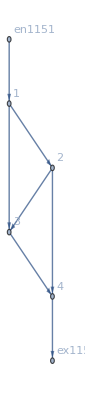

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1158→80.,j1159→80.,j1161→-80.+1. j1153+1. j1154-1. j1160,j1163→0.-1. j1153+1. j1155+1. j1156+1. j1160-1. j1162,j1164→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. j1162,j1165→0.,j1166→0.,jt1167→0.+1. j1160,jt1168→0.,jt1169→-80.+1. j1153+1. j1154-1. j1160,jt1170→0.,jt1171→80.-1. j1154+1. j1160,jt1172→0.+1. j1154-1. j1160,jt1174→0.+1. j1153-1. jt1173,jt1175→0.+1. j1153-1. j1156+1. j1162-1. jt1173,jt1176→0.-1. j1153+1. j1156+1. jt1173,jt1177→0.-1. j1153+1. j1156+1. j1160-1. j1162+1. jt1173,jt1178→0.+1. j1155-1. jt1173,jt1180→0.+1. j1154-1. jt1179,jt1181→0.+1. j1154+1. j1155-1. j1157-1. jt1179,jt1182→0.-1. j1154+1. j1157+1. jt1179,jt1183→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. jt1179,jt1184→0.+1. j1162-1. jt1179,jt1185→-80.+1. j1153-1. j1155+1. j1157-1. j1160+1. j1162,jt1186→80.-1. j1153+1. j1155+1. j1156-1. j1157+1. j1160-1. j1162,jt1187→0.-1. j1153+1. j1155+1. j1156+1. j1160-1. j1162,jt1188→0.+1. j1153-1. j1155-1. j1156+1. j1157-1. j1160+1. j1162,jt1189→0.,jt1190→0.,u1198→0.-1. j1153+1. j1160+1. u1191,u1199→-80.+1. j1153-1. j1160+1. u1192,u1200→0.-1. j1155+1. j1162+1. u1193,u1201→0.-1. j1153+1. j1155+1. j1160-1. j1162+1. u1194,u1202→-80.+1. j1153-1. j1155-1. j1160+1. j1162+1. u1195,u1203→0.+1. u1196,u1204→0.+1. u1197,U2→0.+1. u1196|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```